```mathematica
Manipulate[
Plot[{r*x, Sinh[x]},{x,-1,1}],
{r,0,2}
]
```

```mathematica
Тип бифуркации - суперкритическая "вилка" при r==1
```

```mathematica
Manipulate[
VectorPlot[{1,(r*x - Sinh[x])},{t,-2,2},{x,-2,2}],
{r,0,2}
]
```

```mathematica
Немного грязных хаков: так как Математика отказывается решать уравнения с гиперболическими функциями, заменим синус гиперболический на куб из-за схожего в плане бифуркаций поведения.
Получаем суперкритическая вилку(исходя из предыдущих графиков)
```

{{x→0},{x→-√r},{x→√r}}

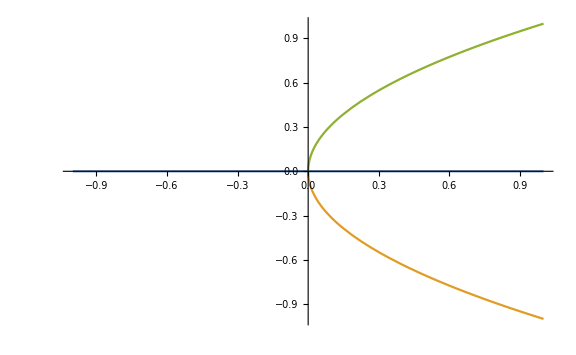

```mathematica
sol = Solve[r*x == x^3, x]
Plot[{x /. sol⟦1⟧, x /. sol⟦2⟧, x /. sol⟦3⟧},{r,-1,1}]
```